```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]={{ⅈ 0.001-0+ω,-t,0,0,0,0,0},{-t,ⅈ 0.001-0+ω,-t,0,0,0,0},{0,-t,ⅈ 0.001-0+ω,-t,0,0,0},{0,0,-t,ⅈ 0.001-0+ω,-t,0,0},{0,0,0,-t,ⅈ 0.001-0+ω,-t,0},{0,0,0,0,-t,ⅈ 0.001-0+ω,-t},{0,0,0,0,0,-t,ⅈ 0.001-0+ω}}
```

```mathematica
T2[t_]:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}
```

```mathematica
T1[t_]:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}}
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:={{0,0,0,0,0,0,0},{0,t,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,t,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,t,0},{0,0,0,0,0,0,0}},T2:={{t,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,t,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,t,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,t}}},Do[J=Inverse[IdentityMatrix[7]-A.T1.Inverse[IdentityMatrix[7]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,0.001,1,0]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,0.001,1,0].T2[1].LEFT[ω,0.001,1,0].T2[1]].g[ω,0.001,1,0]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-g[ω,0.001,1,0].T2[1].LEFT[ω,0.001,1,0].T2[1]].g[ω,0.001,1,0]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SL[ω,0.001,1,0].T1[1].SR[ω,0.001,1,0].T1[1]].SL[ω,0.001,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].SL[ω,0.001,1,0].T1[1]].SR[ω,0.001,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,0.001,1,0]-ConjugateTranspose[IL[ω,0.001,1,0]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,0.001,1,0]-ConjugateTranspose[IR[ω,0.001,1,0]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,0.001,1,0].T1[1].IL[ω,0.001,1,0]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,0.001,1,0]-ConjugateTranspose[Gnonlocal[ω,0.001,1,0]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,0.001,1,0].T1[1].grr[ω,0.001,1,0].T1[1]-T1[1].GNON[ω,0.001,1,0].T1[1].GNON[ω,0.001,1,0]]
```

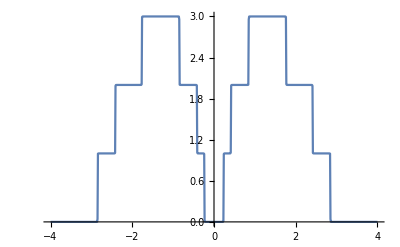
{247.45,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

```mathematica
λ[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{1,7}], μ6=RandomInteger[{1,7}], μ7=RandomInteger[{1,7}],μ8=RandomInteger[{1,7}](*, μ9=RandomInteger[{4,7}], μ10=RandomInteger[{4,7}], μ11=RandomInteger[{4,7}]
Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5[ω_]:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[7]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[7]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[7]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[7]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[7]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[7]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[7]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[7]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[7]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[7]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];(*Clear[m5];m5:=m5=*)η5[1](*ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11},{12,ρ12}};Print[list];{list[[Position[list,Min[list]][[1,1]],1]],Min[list],ListLinePlot[m5],
{μ1,μ3,μ5,μ8},{μ1+μ3+μ5+μ8}}*)]
```

```mathematica
λ[0.5,0,0]
```

2.5647

```mathematica
imp27={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[101]]}[[1,2]]
```

2.80909

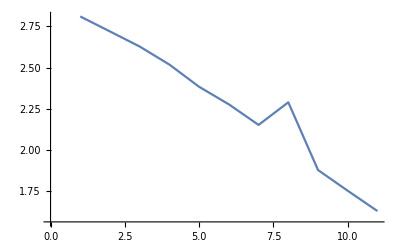

```mathematica
ListLinePlot[{%21,%22,%23,%25,%24,%26,%27,%28,%29,%30,%31}]
```

```mathematica
imp37={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[101]]}[[1,2]]
```

2.71838

```mathematica
imp47={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[101]]}[[1,2]]
```

2.6269

```mathematica
imp67={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[101]]}[[1,2]]
```

2.38323

```mathematica
imp57={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[101]]}[[1,2]]
```

2.51768

```mathematica
imp77={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[101]]}[[1,2]]
```

2.2771

```mathematica
imp87={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[101]]}[[1,2]]
```

2.15249

```mathematica
imp97={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[101]]}[[1,2]]
```

2.28939

```mathematica
imp107={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[101]]}[[1,2]]
```

1.87947

```mathematica
imp117={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[101]]}[[1,2]]
```

1.75383

```mathematica
imp127={Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[101]]}[[1,2]]
```

1.63085

```mathematica
2.71838-1.63085
```

```mathematica
1.0875299999999999/10
```

0.108753

```mathematica
ψ[ω_]:={{4,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[ω]][[2]]},{6,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[ω]][[2]]},{8,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[ω]][[2]]},{10,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[ω]][[2]]},{12,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[ω]][[2]]},{14,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[ω]][[2]]},{16,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[ω]][[2]]},{18,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[ω]][[2]]},{20,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[ω]][[2]]},{22,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[ω]][[2]]},{24,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[ω]][[2]]}}
```

```mathematica
κ[ω_]:=Transpose[ψ[ω]][[2]]
```

```mathematica
Interpolation[{2.8090850848663202,2.718379894308042,2.626899807855988,2.517677778574716,2.383226539989928,2.2771031364522747,2.15248827302051,2.289387139043439,1.8794653930249006,1.7538319185813986,1.630851002825786}]
```

InterpolatingFunction[…]

```mathematica
%112'
```

InterpolatingFunction[…]

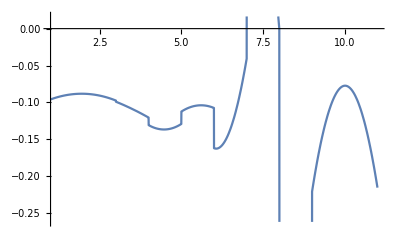

```mathematica
Plot[%113[x],{x,1.,11.}]
```

```mathematica
%113[8]
```

-0.00178905

```mathematica
Export["poi.avi",Manipulate[ListLinePlot[ψ[ω]],{ω,Range[20,300,1]}]]
```

poi.avi

```mathematica
SystemOpen["poi.avi"]
```

```mathematica
Import["poi.avi"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

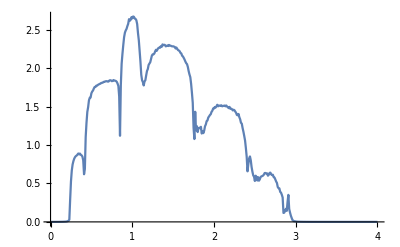

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp1.csv"]]
```

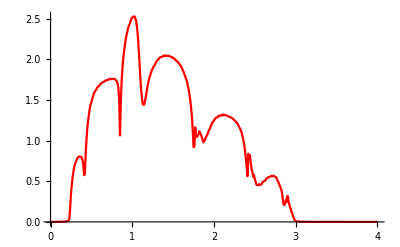

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp1.csv"],PlotStyle->Red]
```

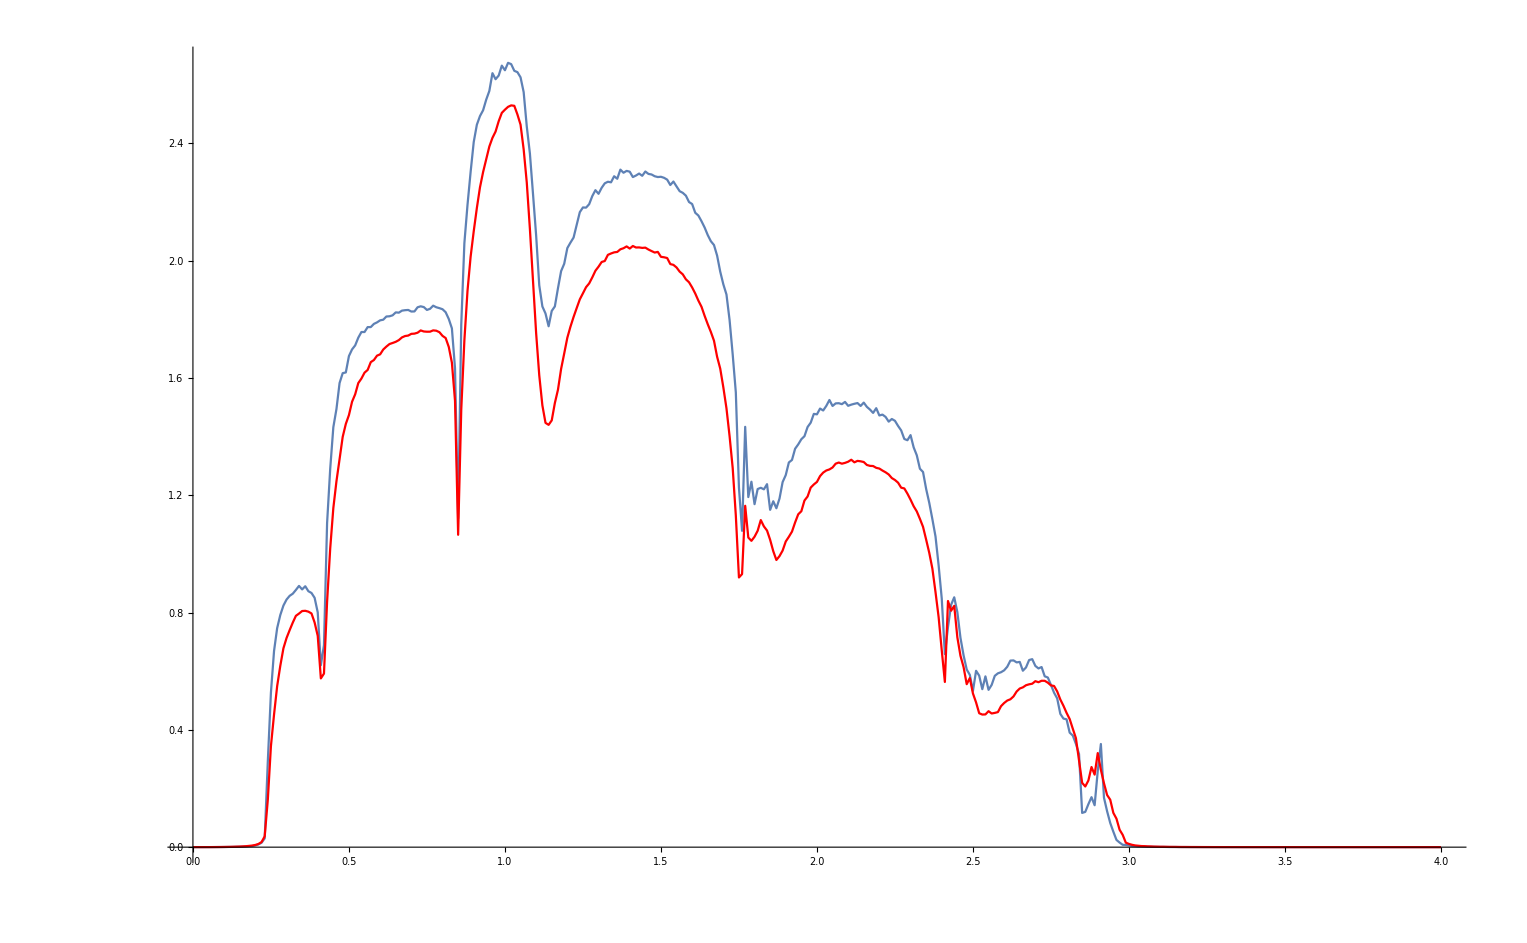

```mathematica
Show[%131,%133]
```

```mathematica
SystemOpen["poi.avi"]
```

```mathematica
ψ[ω_]:=Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[ω]][[2]]-Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[ω]][[2]]
```

```mathematica
ψ[400]
```

-1.03615×10^-6

```mathematica
Table[{.01*ω,ψ[ω]/4},{ω,Range[1,400,1]}]
```

{{0.01,0.0000986338},{0.02,0.000101956},{0.03,0.0000862308},{0.04,0.00006576},{0.05,0.0000345553},{0.06,0.0000576707},{0.07,0.0000359356},{0.08,0.0000143828},{0.09,0.0000224802},{0.1,0.0000183648},{0.11,-0.0000136123},{0.12,0.0000241517},{0.13,0.0000135719},{0.14,0.0000138957},{0.15,-0.0000359686},{0.16,-5.80008×10^-6},{0.17,0.0000114178},{0.18,-0.0000668347},{0.19,-8.38132×10^-6},{0.2,-0.000119764},{0.21,-0.000145136},{0.22,-0.000122589},{0.23,-0.000358646},{0.24,-0.000703286},{0.25,-0.00651859},{0.26,-0.0175502},{0.27,-0.0221618},{0.28,-0.0300076},{0.29,-0.0280399},{0.3,-0.0263073},{0.31,-0.0263499},{0.32,-0.0216783},{0.33,-0.020682},{0.34,-0.0188812},{0.35,-0.0126634},{0.36,-0.0139502},{0.37,-0.0144233},{0.38,-0.0111283},{0.39,-0.0101903},{0.4,-0.00899757},{0.41,-0.00493515},{0.42,0.00070834},{0.43,-0.00517835},{0.44,-0.0170671},{0.45,-0.0283817},{0.46,-0.0307303},{0.47,-0.0345094},{0.48,-0.0340575},{0.49,-0.0327965},{0.5,-0.03443},{0.51,-0.0284724},{0.52,-0.0345797},{0.53,-0.0262076},{0.54,-0.0289883},{0.55,-0.0231865},{0.56,-0.0259821},{0.57,-0.0242754},{0.58,-0.0205081},{0.59,-0.0181594},{0.6,-0.0204114},{0.61,-0.0148096},{0.62,-0.0182469},{0.63,-0.0154337},{0.64,-0.0157843},{0.65,-0.0141494},{0.66,-0.014316},{0.67,-0.0156116},{0.68,-0.0156196},{0.69,-0.014129},{0.7,-0.0148946},{0.71,-0.0118111},{0.72,-0.0109058},{0.73,-0.0144594},{0.74,-0.0114961},{0.75,-0.0118419},{0.76,-0.0127267},{0.77,-0.0102117},{0.78,-0.0117662},{0.79,-0.0117769},{0.8,-0.0122138},{0.81,-0.0143866},{0.82,-0.0133888},{0.83,-0.0128665},{0.84,-0.00907957},{0.85,-0.00989157},{0.86,-0.00546066},{0.87,-0.0212452},{0.88,-0.0303214},{0.89,-0.0265979},{0.9,-0.0397072},{0.91,-0.0431485},{0.92,-0.0449002},{0.93,-0.0477633},{0.94,-0.0433556},{0.95,-0.0381608},{0.96,-0.0439331},{0.97,-0.0377473},{0.98,-0.0377806},{0.99,-0.0306363},{1.,-0.0326821},{1.01,-0.0336128},{1.02,-0.0281233},{1.03,-0.025789},{1.04,-0.0293898},{1.05,-0.021585},{1.06,-0.0261854},{1.07,-0.018758},{1.08,-0.0120624},{1.09,-0.0083588},{1.1,-0.00671288},{1.11,-0.00572082},{1.12,-0.02223},{1.13,-0.0265044},{1.14,-0.0295786},{1.15,-0.0344607},{1.16,-0.0433682},{1.17,-0.042152},{1.18,-0.0523911},{1.19,-0.0550812},{1.2,-0.0534547},{1.21,-0.0558722},{1.22,-0.0555333},{1.23,-0.0501899},{1.24,-0.0490163},{1.25,-0.0508069},{1.26,-0.0440969},{1.27,-0.0465309},{1.28,-0.0415963},{1.29,-0.0372694},{1.3,-0.0371245},{1.31,-0.0295026},{1.32,-0.0367246},{1.33,-0.0321826},{1.34,-0.0392067},{1.35,-0.0317061},{1.36,-0.0330064},{1.37,-0.0302828},{1.38,-0.0312655},{1.39,-0.0289317},{1.4,-0.0293702},{1.41,-0.0286628},{1.42,-0.024649},{1.43,-0.02956},{1.44,-0.0257213},{1.45,-0.0223254},{1.46,-0.0271562},{1.47,-0.0245932},{1.48,-0.0239805},{1.49,-0.0255266},{1.5,-0.0284919},{1.51,-0.0296073},{1.52,-0.0243471},{1.53,-0.0237734},{1.54,-0.0275341},{1.55,-0.0234093},{1.56,-0.0264726},{1.57,-0.0296822},{1.58,-0.0236931},{1.59,-0.0267376},{1.6,-0.025445},{1.61,-0.0285621},{1.62,-0.0265159},{1.63,-0.0302667},{1.64,-0.0263579},{1.65,-0.0282187},{1.66,-0.033784},{1.67,-0.0292961},{1.68,-0.0271464},{1.69,-0.0257882},{1.7,-0.0272331},{1.71,-0.0304596},{1.72,-0.0347403},{1.73,-0.0319238},{1.74,-0.0282169},{1.75,-0.0287083},{1.76,-0.0127599},{1.77,0.00224597},{1.78,-0.0192425},{1.79,-0.0205407},{1.8,-0.021597},{1.81,-0.00615368},{1.82,-0.0133008},{1.83,-0.00758372},{1.84,-0.00601721},{1.85,-0.0214151},{1.86,-0.0175838},{1.87,-0.0133161},{1.88,-0.0141309},{1.89,-0.0256487},{1.9,-0.032869},{1.91,-0.0354399},{1.92,-0.0321552},{1.93,-0.0306621},{1.94,-0.023529},{1.95,-0.02281},{1.96,-0.0202158},{1.97,-0.0135973},{1.98,-0.0149433},{1.99,-0.0124821},{2.,-0.0145208},{2.01,-0.00617313},{2.02,-0.011182},{2.03,-0.0106345},{2.04,-0.00787299},{2.05,-0.0098559},{2.06,-0.0105789},{2.07,-0.00916186},{2.08,-0.00893759},{2.09,-0.0124694},{2.1,-0.0136073},{2.11,-0.0094577},{2.12,-0.0107371},{2.13,-0.00977779},{2.14,-0.0110213},{2.15,-0.00914376},{2.16,-0.00977886},{2.17,-0.00922902},{2.18,-0.0112211},{2.19,-0.0050219},{2.2,-0.00849812},{2.21,-0.0111422},{2.22,-0.0117177},{2.23,-0.0139104},{2.24,-0.00822663},{2.25,-0.0128599},{2.26,-0.00839127},{2.27,-0.0152887},{2.28,-0.00935728},{2.29,-0.00803654},{2.3,-0.0076778},{2.31,-0.00970199},{2.32,-0.0116359},{2.33,-0.00805691},{2.34,-0.0139478},{2.35,-0.0120239},{2.36,-0.010666},{2.37,-0.00924753},{2.38,-0.0168805},{2.39,-0.0163872},{2.4,-0.0137136},{2.41,-0.00765204},{2.42,-0.00529383},{2.43,-0.0317063},{2.44,-0.0162982},{2.45,0.020556},{2.46,0.00551228},{2.47,0.00461353},{2.48,-0.00251709},{2.49,-0.0222948},{2.5,-0.00930307},{2.51,0.00878091},{2.52,0.00980325},{2.53,0.00546882},{2.54,-0.00541937},{2.55,-0.00916003},{2.56,-0.0101293},{2.57,-0.00156338},{2.58,-0.00469604},{2.59,-0.00758025},{2.6,-0.00316599},{2.61,-0.00508991},{2.62,-0.00406623},{2.63,-0.00399099},{2.64,-0.00332136},{2.65,-0.00371168},{2.66,-0.000551497},{2.67,-0.00029995},{2.68,0.0000643474},{2.69,0.00132242},{2.7,0.000315733},{2.71,0.000907628},{2.72,-0.0000336437},{2.73,-0.0010468},{2.74,0.000693713},{2.75,-0.00064459},{2.76,-0.00123358},{2.77,-0.00190488},{2.78,-0.00300316},{2.79,-0.00280446},{2.8,-0.0080388},{2.81,-0.00532238},{2.82,-0.00721925},{2.83,-0.00835234},{2.84,-0.0142235},{2.85,-0.015251},{2.86,-0.0409579},{2.87,-0.0451357},{2.88,-0.0231206},{2.89,0.0310745},{2.9,0.0331062},{2.91,0.011795},{2.92,-0.0147406},{2.93,-0.0111421},{2.94,-0.00621266},{2.95,0.00315895},{2.96,0.0128437},{2.97,0.0122304},{2.98,0.00684039},{2.99,0.00491113},{3.,0.00217965},{3.01,0.00123645},{3.02,0.000361292},{3.03,0.00018977},{3.04,0.000271875},{3.05,0.00013076},{3.06,0.000127193},{3.07,0.0000897279},{3.08,0.000053383},{3.09,0.0000607627},{3.1,0.0000212898},{3.11,0.0000336231},{3.12,0.0000299459},{3.13,0.0000171607},{3.14,0.0000279277},{3.15,0.0000312014},{3.16,0.0000305193},{3.17,0.0000215381},{3.18,0.000018406},{3.19,0.0000233748},{3.2,9.48249×10^-6},{3.21,6.54694×10^-6},{3.22,8.18721×10^-6},{3.23,0.0000145295},{3.24,7.21726×10^-6},{3.25,5.60654×10^-6},{3.26,5.07539×10^-6},{3.27,9.10202×10^-6},{3.28,6.00734×10^-6},{3.29,6.53957×10^-6},{3.3,9.93693×10^-6},{3.31,9.57416×10^-6},{3.32,2.76607×10^-6},{3.33,5.064×10^-6},{3.34,5.0886×10^-6},{3.35,3.69674×10^-6},{3.36,2.19027×10^-6},{3.37,2.18772×10^-6},{3.38,3.84123×10^-6},{3.39,1.69411×10^-6},{3.4,3.27218×10^-6},{3.41,2.32972×10^-6},{3.42,2.41932×10^-6},{3.43,2.06303×10^-6},{3.44,1.33495×10^-6},{3.45,1.73247×10^-6},{3.46,5.17867×10^-7},{3.47,2.5211×10^-7},{3.48,1.24957×10^-6},{3.49,2.31078×10^-6},{3.5,1.98363×10^-6},{3.51,6.94767×10^-7},{3.52,1.54808×10^-6},{3.53,1.51798×10^-6},{3.54,4.3712×10^-7},{3.55,1.28185×10^-6},{3.56,1.20604×10^-6},{3.57,3.91717×10^-7},{3.58,6.03182×10^-7},{3.59,4.04067×10^-7},{3.6,9.22504×10^-7},{3.61,9.11396×10^-7},{3.62,1.02234×10^-6},{3.63,5.77411×10^-7},{3.64,3.15912×10^-7},{3.65,8.68684×10^-7},{3.66,3.09994×10^-7},{3.67,6.39284×10^-7},{3.68,1.74511×10^-7},{3.69,5.05343×10^-7},{3.7,4.57557×10^-7},{3.71,4.11519×10^-7},{3.72,3.03445×10^-7},{3.73,-5.89158×10^-8},{3.74,6.44769×10^-7},{3.75,4.15695×10^-7},{3.76,4.83161×10^-7},{3.77,5.45693×10^-7},{3.78,2.42003×10^-7},{3.79,3.39529×10^-7},{3.8,3.04274×10^-7},{3.81,1.74361×10^-7},{3.82,1.80746×10^-7},{3.83,2.75171×10^-7},{3.84,-9.28132×10^-8},{3.85,1.1533×10^-7},{3.86,2.61249×10^-7},{3.87,4.52748×10^-7},{3.88,1.4706×10^-7},{3.89,1.42911×10^-7},{3.9,1.17745×10^-7},{3.91,2.26269×10^-7},{3.92,2.33246×10^-7},{3.93,-3.10775×10^-8},{3.94,-2.08929×10^-8},{3.95,7.25461×10^-8},{3.96,1.36923×10^-7},{3.97,1.11089×10^-7},{3.98,1.53938×10^-7},{3.99,3.04139×10^-8},{4.,8.6577×10^-8}}

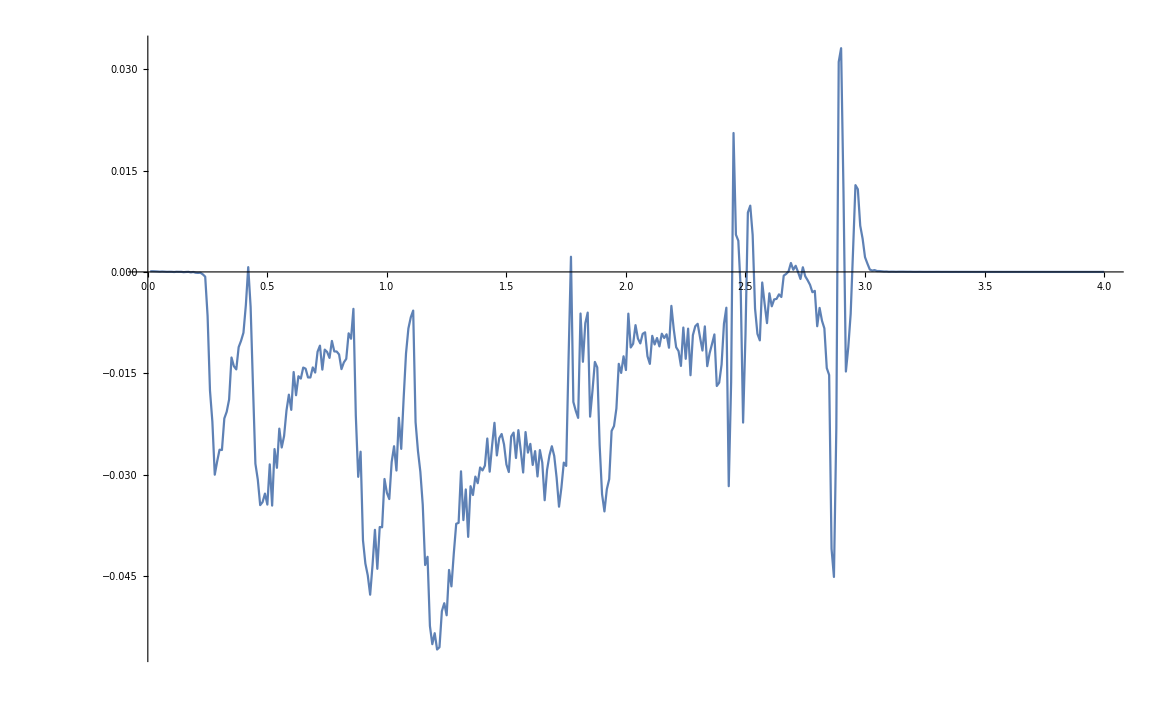

```mathematica
ListPlot[%166,Joined->True]
```

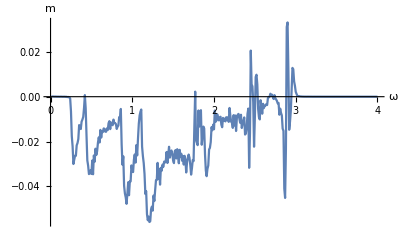

```mathematica
Show[%167,AxesLabel->{HoldForm[ω],HoldForm[m]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

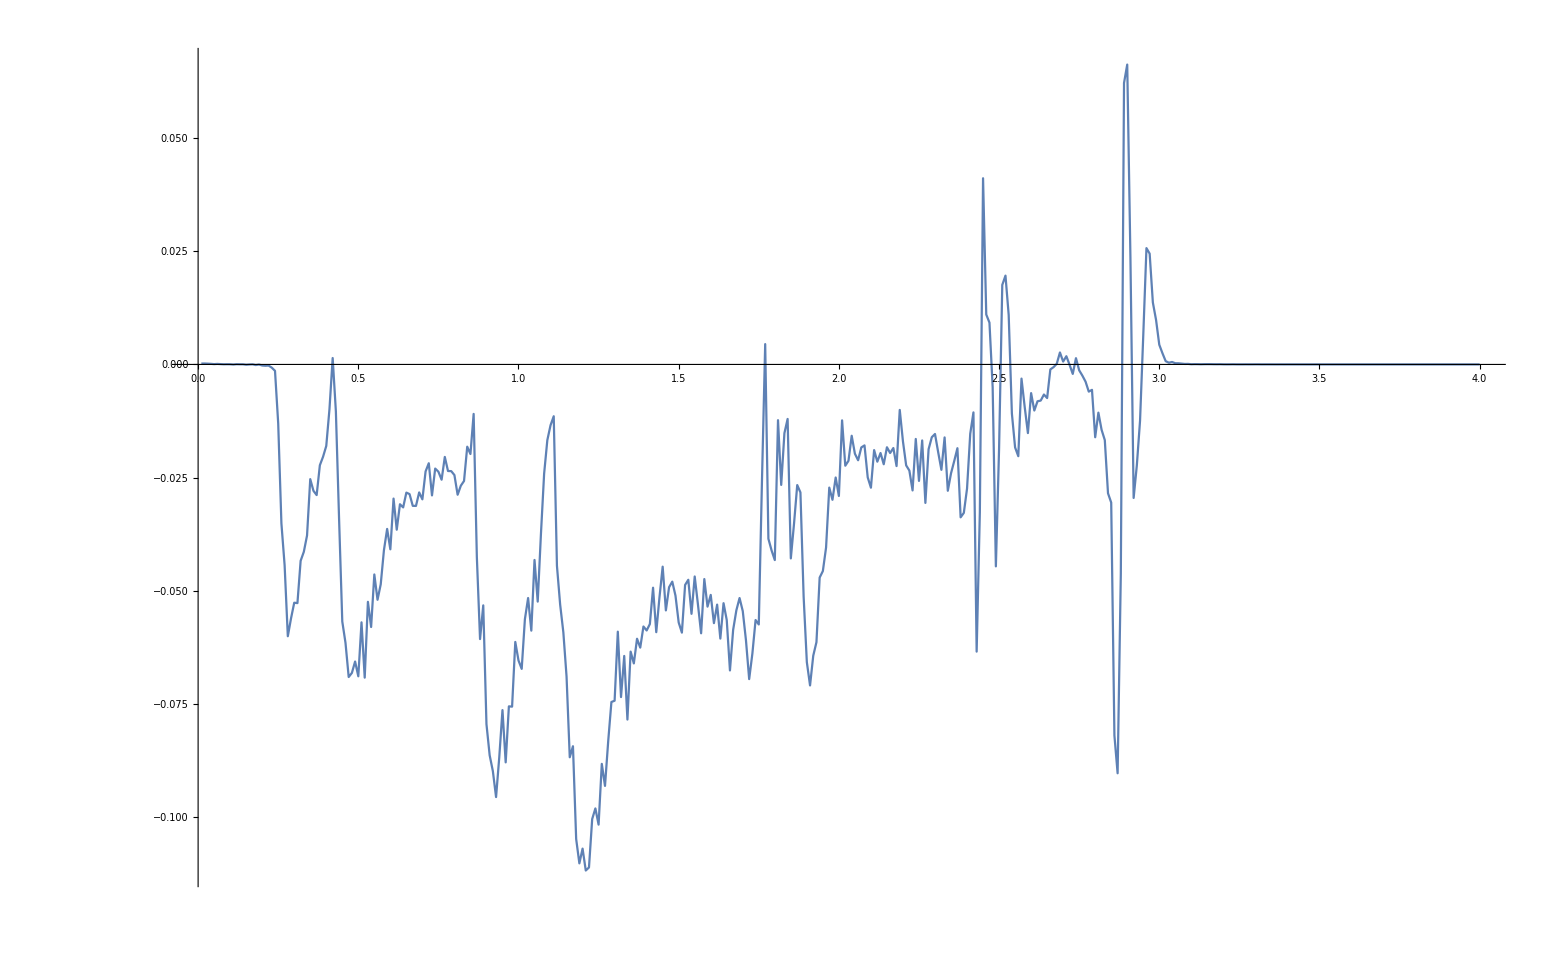

```mathematica
ListPlot[%164,Joined->True]
```

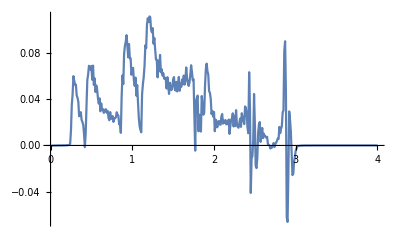

```mathematica
ListPlot[%162,Joined->True]
```

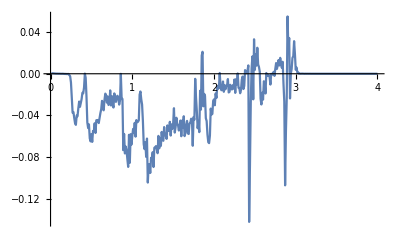

```mathematica
ListPlot[%159,Joined->True]
```

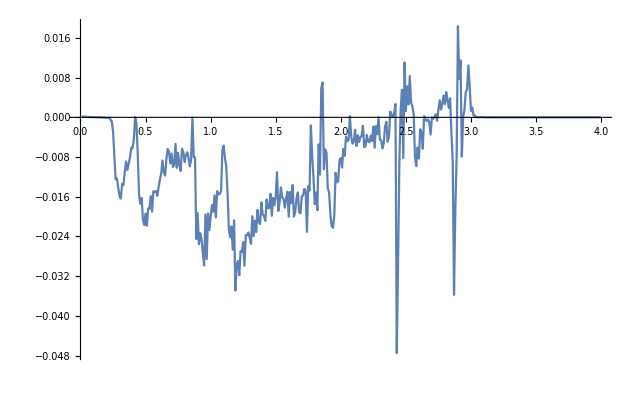

```mathematica
ListPlot[%157,Joined->True]
```

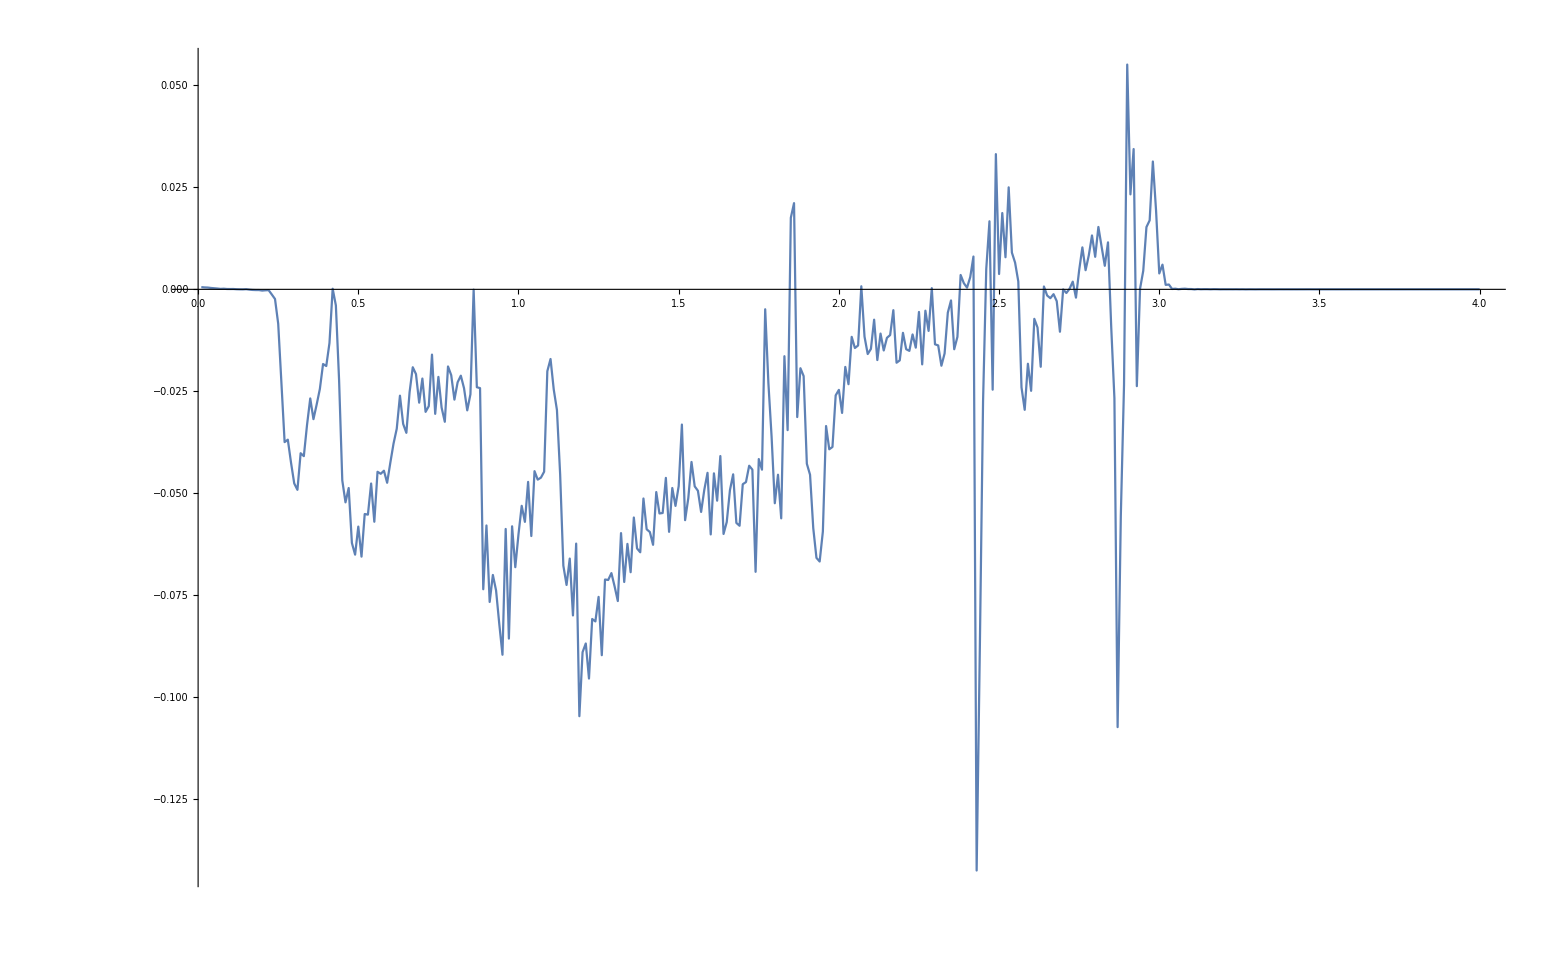

```mathematica
ListPlot[%155,Joined->True]
```

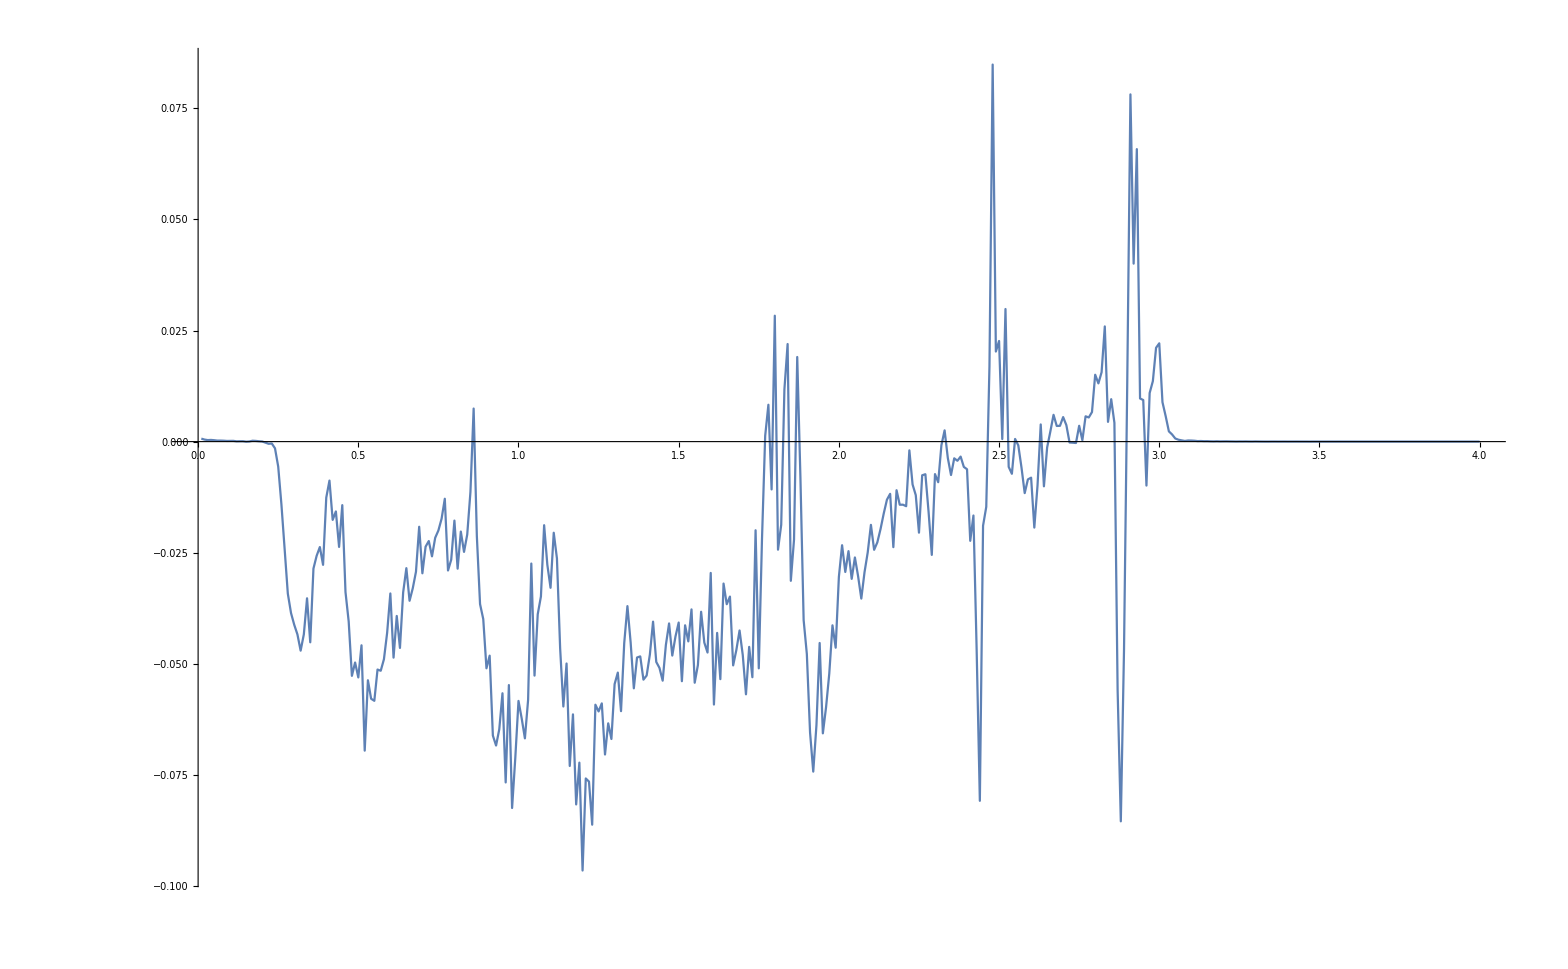

```mathematica
ListPlot[%152,Joined->True]
```

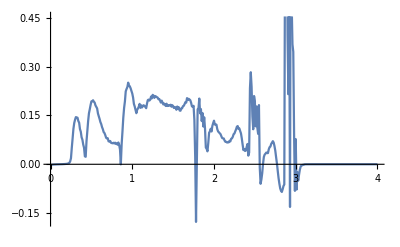

```mathematica
ListPlot[%148,Joined->True]
```

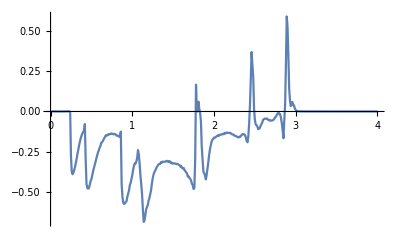

```mathematica
ListPlot[%142,Joined->True]
```

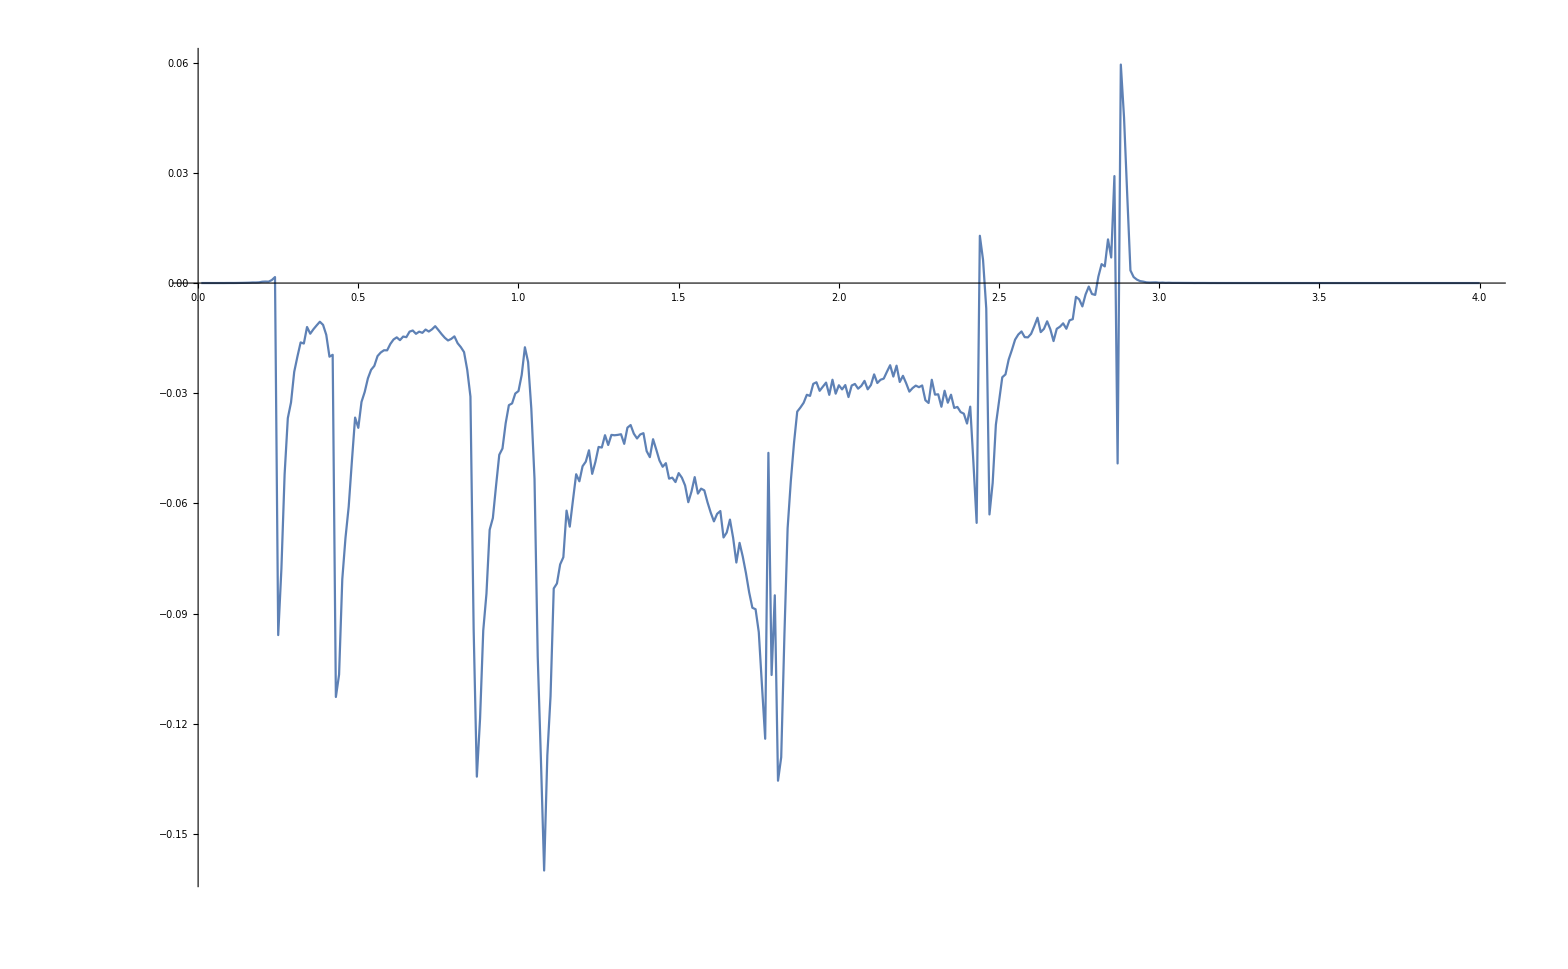

```mathematica
ListPlot[%138,Joined->True]
```

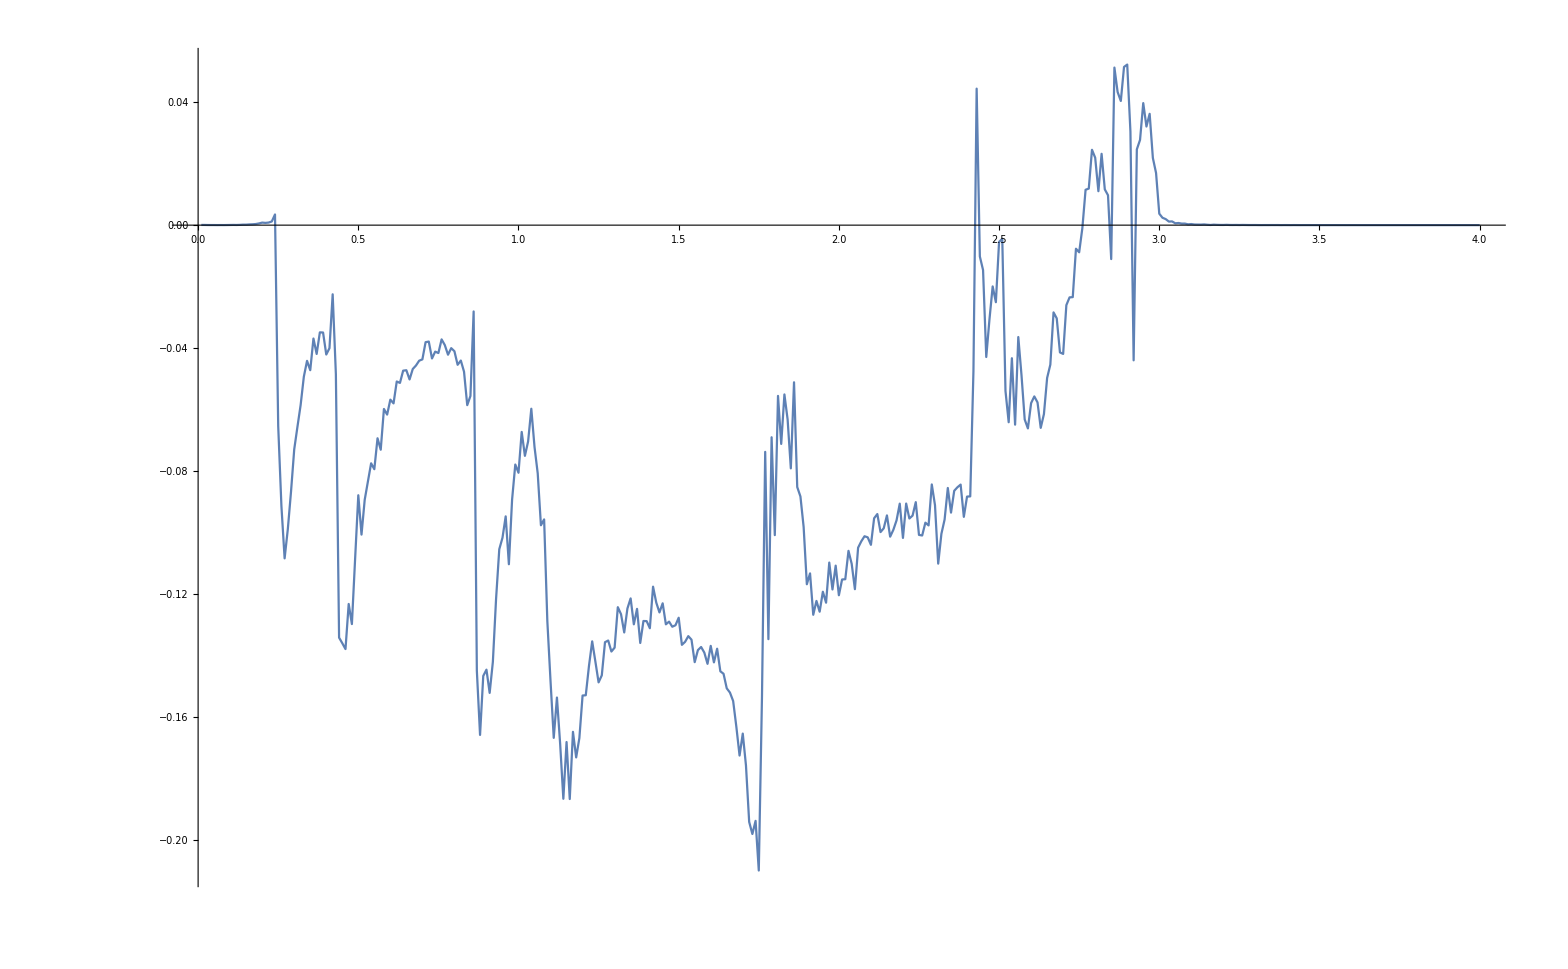

```mathematica
ListPlot[%129,Joined->True]
```

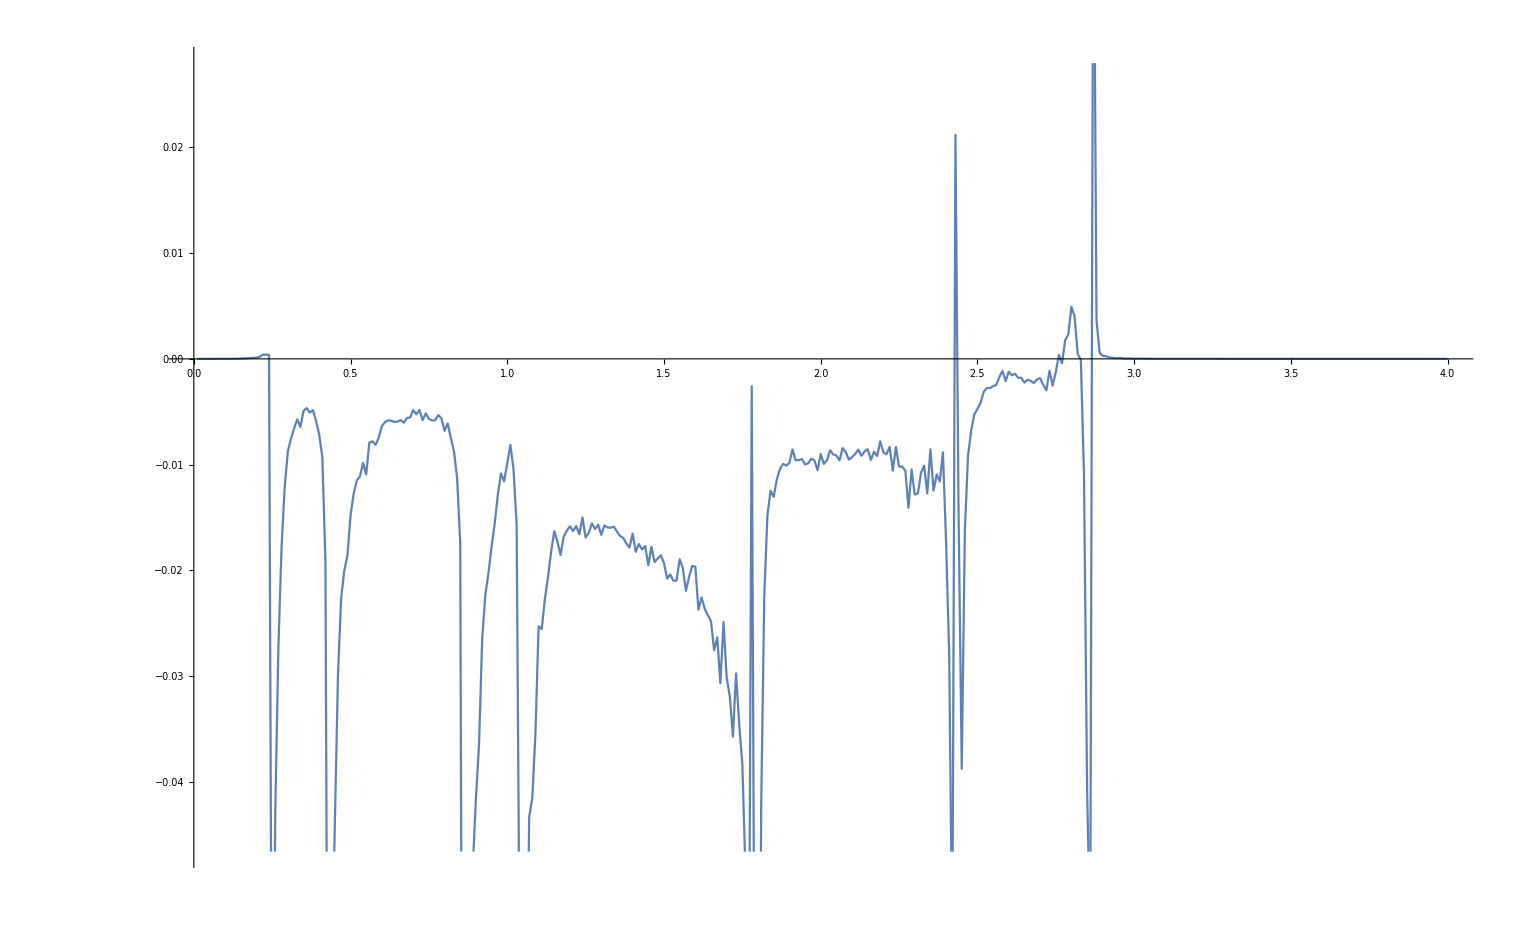

```mathematica
ListPlot[%125,Joined->True]
```

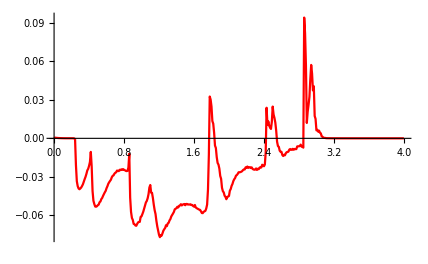

```mathematica
ListPlot[%103,Joined->True,PlotStyle->Red]
```

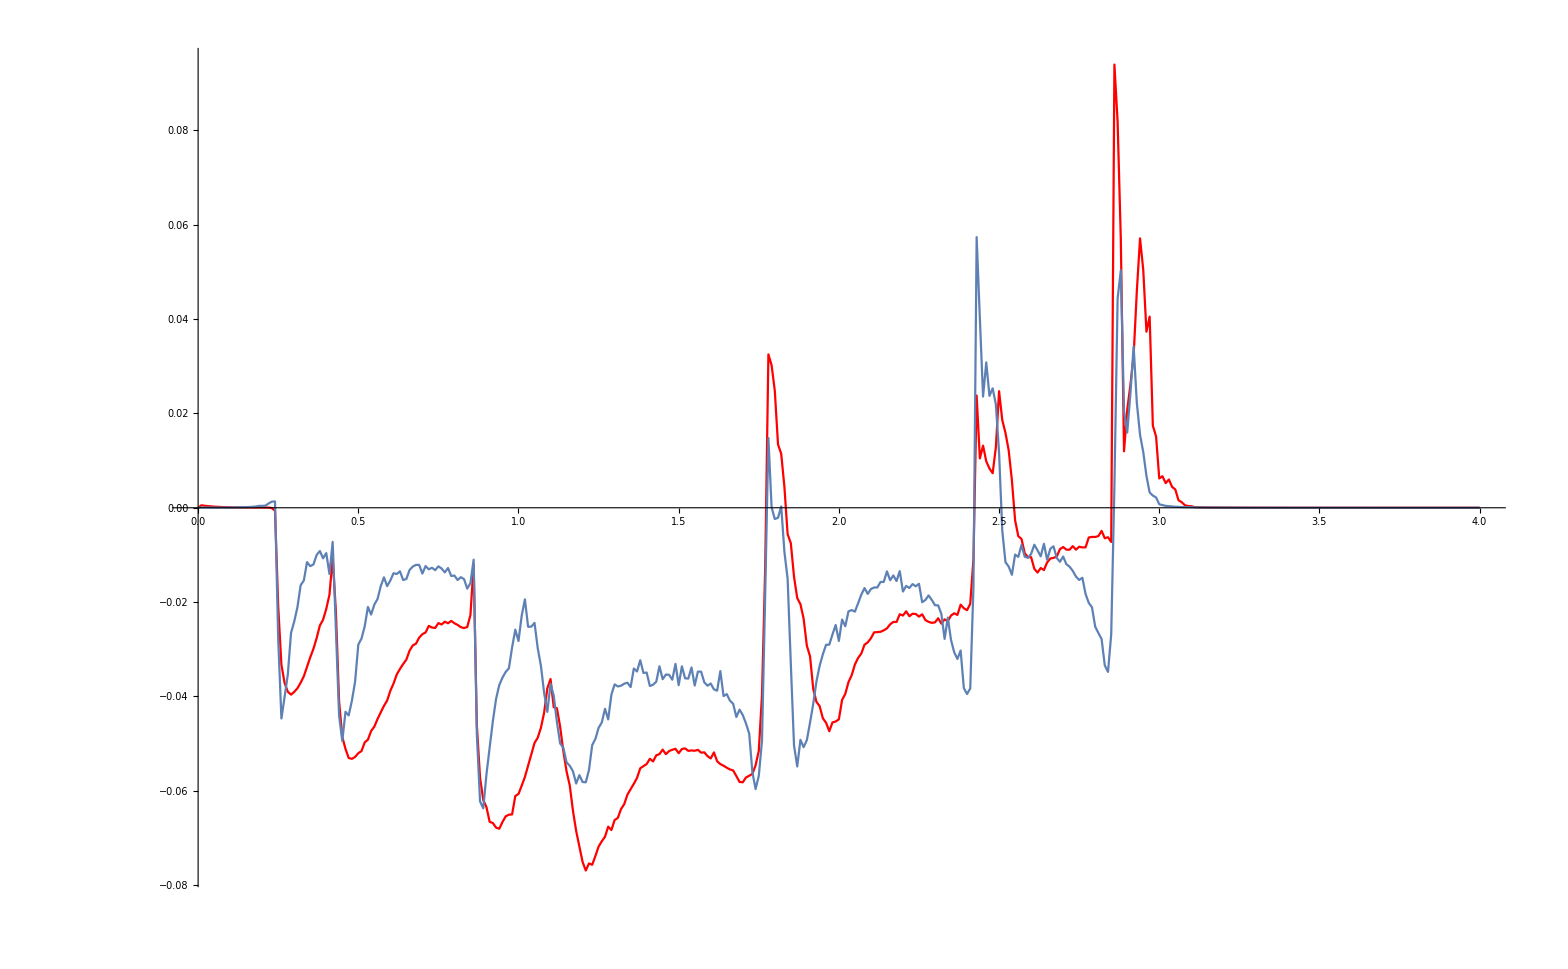

```mathematica
Show[%105,%100]
```

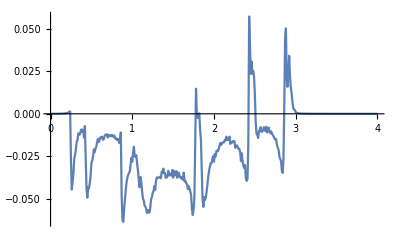

```mathematica
ListPlot[%99,Joined->True]
```

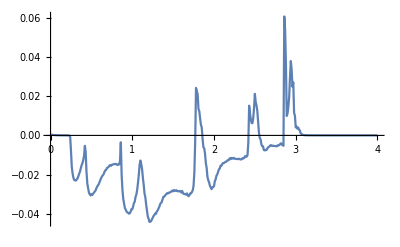

```mathematica
ListPlot[%80,Joined->True]
```

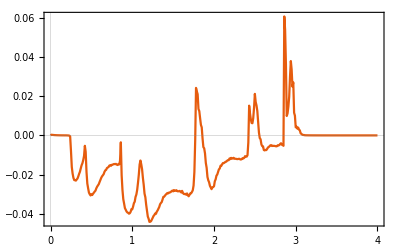

```mathematica
ListPlot[%80,PlotTheme->"Scientific",Joined->True]
```

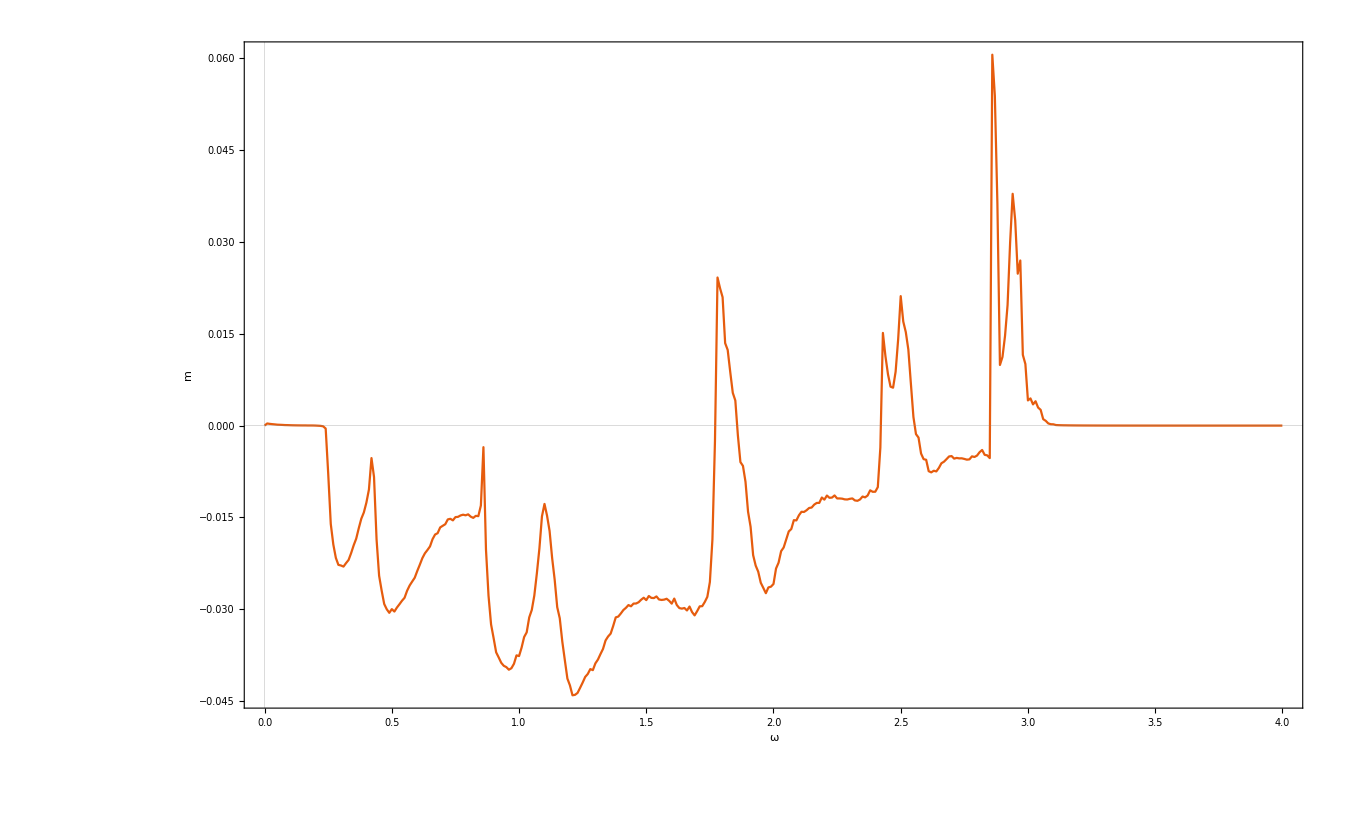

```mathematica
Show[%82,FrameLabel->{{HoldForm[m],None},{HoldForm[ω],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

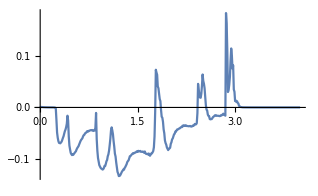

```mathematica
ListPlot[%78,Joined->True]
```

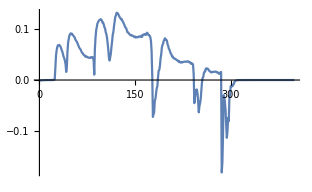

```mathematica
ListPlot[%74,Joined->True]
```

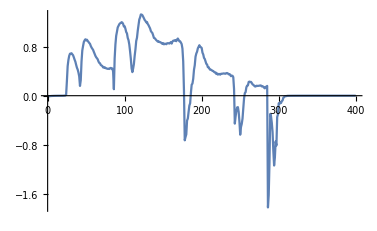

```mathematica
ListPlot[%62,Joined->True]
```

Part::pkspec1: The expression 0.200076 cannot be used as a part specification.

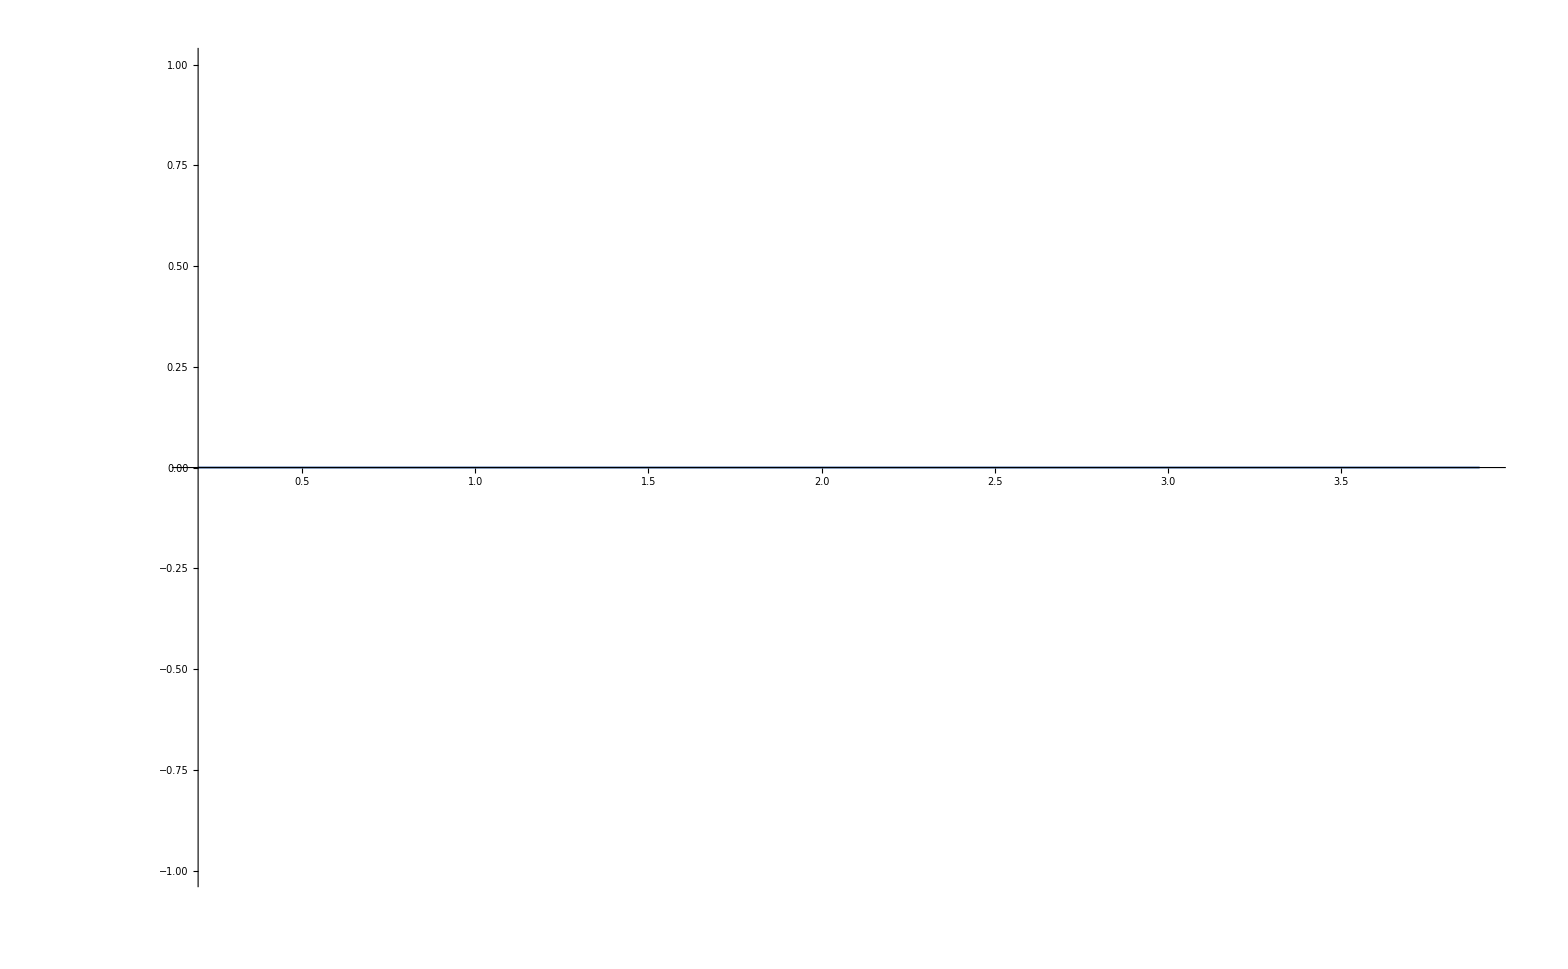

```mathematica
Plot[ψ[ω],{ω,0.2,3.9}]
```

```mathematica
{{4,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"]},{6,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"]},{8,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"]},{10,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"]},{12,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"]},{14,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"]},{16,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"]},{18,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"]},{20,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"]},{22,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"]},{24,Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"]}}
```

{{4,{{0.,0.0000278312},{0.01,0.0000261856},{0.02,0.0000248702},{0.03,0.0000322542},{0.04,0.0000435483},{0.05,0.0000667509},{0.06,0.0000815968},{0.07,0.000109589},{0.08,0.000163075},{0.09,0.000206958},{0.1,0.000267955},{0.11,0.00037524},{0.12,0.000425663},{0.13,0.000522123},{0.14,0.000743983},{0.15,0.000824763},{0.16,0.00115228},{0.17,0.00154613},{0.18,0.00203018},{0.19,0.00266361},{0.2,0.0036726},{0.21,0.00517573},{0.22,0.00958421},{0.23,0.0242427},{0.24,0.431561},352,{3.77,2.63816×10^-6},{3.78,1.95298×10^-6},{3.79,1.74176×10^-6},{3.8,1.67517×10^-6},{3.81,1.54701×10^-6},{3.82,1.68971×10^-6},{3.83,1.84357×10^-6},{3.84,1.51195×10^-6},{3.85,1.26195×10^-6},{3.86,1.48668×10^-6},{3.87,1.20297×10^-6},{3.88,1.4925×10^-6},{3.89,1.23604×10^-6},{3.9,1.38002×10^-6},{3.91,1.55363×10^-6},{3.92,8.55897×10^-7},{3.93,1.125×10^-6},{3.94,9.83962×10^-7},{3.95,1.26147×10^-6},{3.96,1.21844×10^-6},{3.97,8.83378×10^-7},{3.98,8.57297×10^-7},{3.99,9.04525×10^-7},{4.,7.92311×10^-7}}},9,{24,{1}}}
 |  |  |  |